# Finite Difference Methods

## Fully implicit Scheme with Richtmyer modification

Implicit method with Richtmyer modification for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]

Clear[makeRichtmyerDiagonals];

makeRichtmyerDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[25/12+2*α,{m-2}];
{x,y,z}];

Clear[makeMatrix];
makeMatrix[x_,y_,z_]:=Module[{n=Length[y]},
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},n]
]
```

```mathematica
{x,y,z}=makeDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻,1.+2. 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

```mathematica
MatrixForm[makeMatrix[x,y,z]]
```

(1.+2. 𝔻 | -𝔻 | 0 | 0 | 0
-𝔻 | 1.+2. 𝔻 | -𝔻 | 0 | 0
0 | -𝔻 | 1.+2. 𝔻 | -𝔻 | 0
0 | 0 | -𝔻 | 1.+2. 𝔻 | -𝔻
0 | 0 | 0 | -𝔻 | 1.+2. 𝔻)

```mathematica
{x,y,z}=makeRichtmyerDiagonals[7,𝔻]
```

{{-𝔻,-𝔻,-𝔻,-𝔻},{25/12+2 𝔻,25/12+2 𝔻,25/12+2 𝔻,25/12+2 𝔻,25/12+2 𝔻},{-𝔻,-𝔻,-𝔻,-𝔻}}

```mathematica
MatrixForm[makeMatrix[x,y,z]]
```

(25/12+2 𝔻 | -𝔻 | 0 | 0 | 0
-𝔻 | 25/12+2 𝔻 | -𝔻 | 0 | 0
0 | -𝔻 | 25/12+2 𝔻 | -𝔻 | 0
0 | 0 | -𝔻 | 25/12+2 𝔻 | -𝔻
0 | 0 | 0 | -𝔻 | 25/12+2 𝔻)

## Set Up Solution

### LinearSolve Solution

```mathematica
Clear[implicitSolveRichtmeyer];

implicitSolveRichtmeyer[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,c,solveStart,solveRest},

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];

solveStart:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

c=NestList[solveStart,initial,3];

{x,y,z}=makeRichtmyerDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];

solveRest:=Module[{temp,b},

b=Flatten@MapThread[{4*#4-3*#3+(4./3.)*#2-0.25*#1}&,Take[c,-4]];
b=b⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
c=Join[c,{Flatten[{0.,LinearSolve[mat,b],1.}]}]]&;

Nest[solveRest,c,n-4]
]
```

## Set Parameter Values

```mathematica
Clear[𝒟,time,n,m,Δt,Δx,𝔻,c];

𝒟=10^-5;
time=0.1;
n=100;
𝔻=2.;
m=Ceiling[6*√(𝔻*(n-1))];
Δt=time/(n-1)//N;
Δx=√((𝒟*Δt)/𝔻);
```

## Solve

LinearSolve solution

```mathematica
Clear[c];

Timing[
c=implicitSolveRichtmeyer[m,n,𝔻];
c=Rest[c];]
```

{1.45664,Null}

```mathematica
ListPlot3D[Transpose@c,PlotRange->All]
```

-Graphics3D-

### Comparison with analytical result

```mathematica
p=10;(*enter a time increment*)

cb=Table[Erf[((j-1)*Δx)/(2*Sqrt[𝒟*Δt*(p-1)])]/c⟦p-1,j⟧,{j,2,m-1}]
```

{0.986193,0.985395,0.986369,0.988483,0.990865,0.993168,0.995314,0.997254,0.998916,1.00023,1.00118,1.00176,1.00202,1.00204,1.00189,1.00165,1.00136,1.00107,1.00081,1.00059,1.00042,1.00029,1.00019,1.00012,1.00008,1.00005,1.00003,1.00002,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Plot Current v. Time

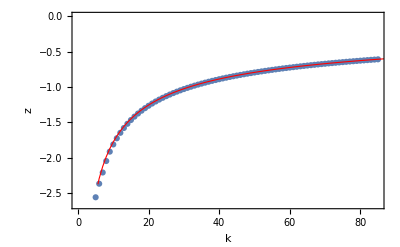

```mathematica
Clear[i,z];
i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```